### One conclusion of this baby look at H1(u1,u2) is that for a lower bound less than 0 or an upper bound greater than 1, this integral is pretty rude.

NIntegrate::precw: The precision of the argument function (√(1-t) t^0.000377929) is less than WorkingPrecision (18.).

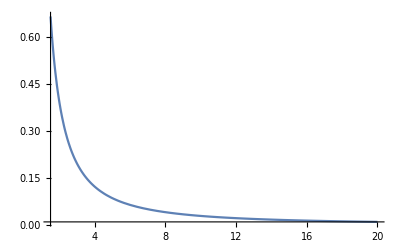

```mathematica
Plot[Aich1[0,1,kappa],{kappa,3/2,20},PlotRange->Full]
```

NIntegrate::precw: The precision of the argument function (√(1-t) t^0.000128696) is less than WorkingPrecision (18.).

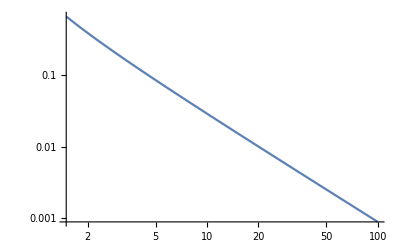

```mathematica
LogLogPlot[Aich1[0,1,kappa],{kappa,3/2,100},PlotRange->Full]
```

```mathematica
kappaList={1501/1000,155/100,16/10,18/10,19/10,20/10,25/10,31/10,4,6,10,25,45,80,101};
kappaLen=Length[kappaList];
```

```mathematica
data=Table[{kappaList[[i]],Log10[Aich1[0,1,kappaList[[i]]]]},{i,kappaLen}]
```

{{1501/1000,-0.17664706712650677},{31/20,-0.20328634014368503},{8/5,-0.22933638546118663},{9/5,-0.32383595351139571},{19/10,-0.36622523294478246},{2,-0.40594011429780973},{5/2,-0.574031267727718852},{31/10,-0.730547406899058897},{4,-0.911090092618591256},{6,-1.1909307892119843},{10,-1.53560509041419193},{25,-2.14276247573155744},{45,-2.52862767592753485},{80,-2.90504576217966531},{101,-3.05731929894005333}}

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-0.58858115972506656-0.029456295873719639 x]

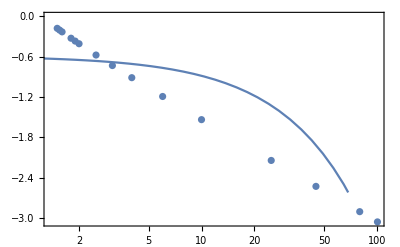

```mathematica
Show[ListLogLinearPlot[data],LogLinearPlot[lm[x],{x,0,100}],Frame->True]
```

### See what happens if lower bound is negative:

```mathematica
data=Table[{kappaList[[i]],Aich1[-1,1,kappaList[[i]]]},{i,kappaLen}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0038841859426028883935637616244378614768237627259616262250083639500112}. NIntegrate obtained 1.8836465464188093061242536419507147966705092361876988162586689708305+0.0038259462924824342427983916172057869533492741340845444289788060333634 ⅈ and 9.8824001830995587637916166643917599621773096795052711028572422729223×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0038841859426028883935637616244378614768237627259616262250083639500112}. NIntegrate obtained 1.7776263999431763923739271577401674270062544830989157144353915801614+0.18236785417550676424833022802158215351121096670919133026174582880078 ⅈ and 3.2681782222394193143812136545560978343497110752742336867667033505279×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0038841859426028883935637616244378614768237627259616262250083639500112}. NIntegrate obtained 1.6522696894547462220748666015766084888221173747399357787698054775993+0.34523541230599105203883083854515874831192750026090757550859310577616 ⅈ and 3.7351643643766912170849569446724757223055547613984224352464584621488×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1501/1000,1.88364654641880931+0.00382594629248243 ⅈ},{31/20,1.77762639994317639+0.18236785417550676 ⅈ},{8/5,1.65226968945474622+0.34523541230599105 ⅈ},{9/5,1.03785584671901272+0.7755012577940106 ⅈ},{19/10,0.70701126830895391+0.851619233867687645 ⅈ},{2,0.39269908660534402+0.840316779931526479 ⅈ},{5/2,-0.377123616632825346},{31/10,0.34164430204111887-0.479103450108326628 ⅈ},{4,0.12271846303060389+0.380450122390286221 ⅈ},{6,0.064427193091163483+0.246876766335422434 ⅈ},{10,0.029133650744921826+0.145238026660828078 ⅈ},{25,0.0071984256654433036-0.0571515995667183351 ⅈ},{45,0.0029605494812321277-0.0316045102148483967 ⅈ},{80,0.001244383482541794+0.0177334339389562236 ⅈ},{101,0.0008763562757249438-0.0140370320358979711 ⅈ}}

```mathematica
data=Table[{kappaList[[i]],Aich1[-0.1,1,kappaList[[i]]]},{i,kappaLen}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.00096442726843158357485872677449789491171448254451254720038721238037394}. NIntegrate obtained 0.7679369362330590510633606629880541598154632911336283901697620228331+0.0003209283939404325266863906744466263954689250617716741764840424438091 ⅈ and 5.6448866775538275788643203434628439053474377029512047093187422169131×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.000964427268431583575}. NIntegrate obtained 0.712153906006055813+0.0136162096594033251 ⅈ and 0.0000194482384482935971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.000964427268431583575}. NIntegrate obtained 0.660196034089061438+0.0228938815423293549 ⅈ and 0.0000223046211681859324 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1501/1000,0.767936936233059051+0.00032092839394043 ⅈ},{31/20,0.712153906006055813+0.0136162096594033251 ⅈ},{8/5,0.660196034089061438+0.0228938815423293549 ⅈ},{9/5,0.497712691881301853+0.03205852652608531 ⅈ},{19/10,0.439342919414828405+0.02782075077629332 ⅈ},{2,0.392699143364508079+0.02170379733170759 ⅈ},{5/2,0.261503006143757785},{31/10,0.186283277073610746-0.00095138127997537 ⅈ},{4,0.122718463032423406+0.0000937954557389117 ⅈ},{6,0.0644271930911284542+5.987793852879×10^-7 ⅈ},{10,0.0291336507449218721+3.47651443×10^-11 ⅈ},{25,0.00719842566544330401},{45,0.00296054948123212775},{80,0.00124438348254179403},{101,0.000876356275724943815}}

### Try exceeding upper bound = 1

```mathematica
data=Table[{kappaList[[i]],Aich1[0,0.5,kappaList[[i]]]},{i,kappaLen}]
```

{{1501/1000,0.430199889974928942},{31/20,0.394855406575206636},{8/5,0.362655277244203532},{9/5,0.26340708166824778},{19/10,0.226788928473292834},{2,0.196349540849362077},{5/2,0.101675084389805578},{31/10,0.0505440453435437351},{4,0.0196925648487371603},{6,0.00304692987893106719},{10,0.00010749997563551657},{25,1.23984531096632118×10^-9},{45,6.45635471916548763×10^-16},{80,1.04690241118740369×10^-26},{101,3.94392155089050888×10^-33}}